# < Monitoring the development and spread of cities >

< Ahmed Elbanna>

< Christopher Wolfram>

## The plan so far

get set of historical satellite images

mark the differences, measure them somehow

produce a rate of change (with visualizing)

apply regression tree on the differences to model them and predict the spread in the upcoming years

Maybe try to learn the distribution either of the full set of differences between images or the rates (or both)

Christopher’s additions or modifications on the plan:

## Historical images

Historical images are collected by Google Earth Pro desktop application. It has a function that allows exploring of the same frame over time. Test data is collected above the state Dubai and its neighbourhood.
UPDATE: I added the set of images in the draft folder so that we can import them easily.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
imgList=Import["*.jpg"];
```

```mathematica
diffList=Differences[imgList];
```

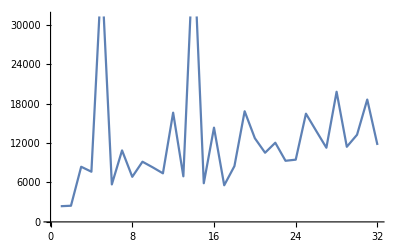

```mathematica
ImageMeasurements[Binarize[#,.1],"Total"]&/@diffList//ListLinePlot
```

```mathematica
Accumulate[Binarize[#,.1]&/@diffList]//ListAnimate
```

Ok there are some anomalies here, I think it is because of the wind (specially the area above the sea line and some wind effects on the sands at the bottom area of the map)

### Problem1: I need to figure a way to avoid or remove anomalies

Suggested solutions will be introduced in this subsection